```mathematica
(*Takehome Assignment Q5*)
```

```mathematica
Remove["Global`*"]
```

```mathematica
ℒ:=1/2(Subscript[m, 1]+Subscript[m, 2])Subscript[l, 1]^2(θ1'[t])^2+1/2 Subscript[m, 2] Subscript[l, 2]^2(θ2'[t])^2+Subscript[m, 2] Subscript[l, 1] Subscript[l, 2](θ1'[t])(θ2'[t])Cos[θ2[t]-θ1[t]]+(Subscript[m, 1]+Subscript[m, 2])g Subscript[l, 1] Cos[θ1[t]]+Subscript[m, 2] g Subscript[l, 2] Cos[θ2[t]]
(*Lagrangian for a double pendulum*)
```

```mathematica
A=NDSolve[{D[D[ℒ, θ1'[t]],t]==D[ℒ, θ1[t]],
D[D[ℒ, θ2'[t]],t]==D[ℒ, θ2[t]],
θ1[0]==Pi/2,θ2[0]==Pi/2,θ1'[0]==0,θ2'[0]==0}/.{Subscript[m, 1]->1,Subscript[m, 2]->1,Subscript[l, 1]->1,Subscript[l, 2]->1,g->9.8},{θ1[t],θ2[t]},{t,0,100}]
(*numerically solving the equations of motion and storing as a list. the initial conditions can be changed from here*)
```

{{θ1[t]→InterpolatingFunction[{{0., 100.}}, <>][t],θ2[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

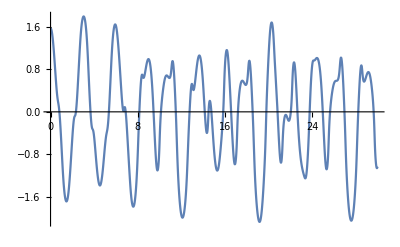

```mathematica
Plot[θ1[t]/.A,{t,0,30}]
```

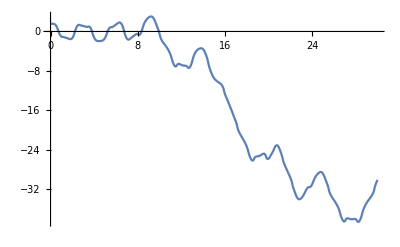

```mathematica
Plot[θ2[t]/.A,{t,0,30}]
```

```mathematica
(*these plots come out different for different intial conditions. the behaviour is chaotic. as we make Subscript[m, 1] much larger than Subscript[m, 2], or Subscript[l, 1] much larger than l_(2,) the trajectory of the first mass approaches that of a simple pendulum, as its moment of inertia becomes large
the same holds for Subscript[m, 2]*)
```

```mathematica
Solve[{D[D[ℒ, θ1'[t]],t]==D[ℒ, θ1[t]],D[D[ℒ, θ2'[t]],t]==D[ℒ, θ2[t]]},{θ1''[t],θ2''[t]}]
(*algebraically solving the equations of motion for θ1''[t] and θ2''[t]*)
```

{{θ1''[t]→-((g Sin[θ1[t]] m_1+g Sin[θ1[t]] m_2-g Cos[θ1[t]-θ2[t]] Sin[θ2[t]] m_2+Cos[θ1[t]-θ2[t]] Sin[θ1[t]-θ2[t]] l_1 m_2 θ1'[t]^2+Sin[θ1[t]-θ2[t]] l_2 m_2 θ2'[t]^2)/(l_1 (m_1+m_2-Cos[θ1[t]-θ2[t]]^2 m_2))),θ2''[t]→(g Cos[θ1[t]-θ2[t]] Sin[θ1[t]] m_1-g Sin[θ2[t]] m_1+g Cos[θ1[t]-θ2[t]] Sin[θ1[t]] m_2-g Sin[θ2[t]] m_2+Sin[θ1[t]-θ2[t]] l_1 m_1 θ1'[t]^2+Sin[θ1[t]-θ2[t]] l_1 m_2 θ1'[t]^2+Cos[θ1[t]-θ2[t]] Sin[θ1[t]-θ2[t]] l_2 m_2 θ2'[t]^2)/(l_2 (m_1+m_2-Cos[θ1[t]-θ2[t]]^2 m_2))}}

```mathematica
FullSimplify[%[[1]]]
```

{θ1''[t]→-(g Sin[θ1[t]] m_1+Sin[θ1[t]-θ2[t]] m_2 (g Cos[θ2[t]]+Cos[θ1[t]-θ2[t]] l_1 θ1'[t]^2+l_2 θ2'[t]^2))/(l_1 (m_1+Sin[θ1[t]-θ2[t]]^2 m_2)),θ2''[t]→(Sin[θ1[t]-θ2[t]] ((m_1+m_2) (g Cos[θ1[t]]+l_1 θ1'[t]^2)+Cos[θ1[t]-θ2[t]] l_2 m_2 θ2'[t]^2))/(l_2 (m_1+Sin[θ1[t]-θ2[t]]^2 m_2))}

```mathematica
ϕ1''[t]=(-(g Subscript[m, 1] θ1[t]+Subscript[m, 2] g(θ1[t]-θ2[t])))/(Subscript[l, 1] Subscript[m, 1])
```

-(g m_1 θ1[t]+g m_2 (θ1[t]-θ2[t]))/(l_1 m_1)

```mathematica
ϕ2''[t]=((θ1[t]-θ2[t])(Subscript[m, 2]+Subscript[m, 1])g)/(Subscript[m, 1] Subscript[l, 2])
```

(g (m_1+m_2) (θ1[t]-θ2[t]))/(l_2 m_1)

```mathematica
(*ϕ1''[t] and ϕ2''[t] are θ1''[t] and θ2''[t] respectively with small angle approximation and the first derivatives put to zero.
we can infer that the matrix M={{a1,a2},{a3,a4}} from the above 2 equations. M is such that
{θ1''[t],θ2''[t]}==1/α M {θ1[t],θ2[t]}. Here α=1.*)
```

```mathematica
M=g/Subscript[m, 1]{{(-(Subscript[m, 1]+Subscript[m, 2]))/Subscript[l, 1],Subscript[m, 2]/Subscript[l, 1]},{(Subscript[m, 1]+Subscript[m, 2])/Subscript[l, 2],(-(Subscript[m, 1]+Subscript[m, 2]))/Subscript[l, 2]}}
```

{{-(g (m_1+m_2))/(l_1 m_1),(g m_2)/(l_1 m_1)},{(g (m_1+m_2))/(l_2 m_1),-(g (m_1+m_2))/(l_2 m_1)}}

```mathematica
em=FullSimplify[Eigenvalues[M]]/.{Subscript[m, 1]->1,Subscript[m, 2]->1,Subscript[l, 1]->1,Subscript[l, 2]->1,g->9.8}
(*negatives of squares of normal mode frequencies. one comes out to be high whereas the other comes out to be low. the mass and length can be varied from here*)
```

{-33.4593,-5.74071}

```mathematica
FullSimplify[Eigenvectors[M]] /.{Subscript[m, 1]->1,Subscript[m, 2]->1,Subscript[l, 1]->1,Subscript[l, 2]->1,g->9.8}
(*normal modes*)
```

{{-1/(√2),1},{1/(√2),1}}

```mathematica
Sapprox11=DSolve[{θ1''[t]==em[[1]]θ1[t],θ1[0]==Subscript[θ11, 0],θ1'[0]==0},{θ1[t]},{t,0,50}] (*higher frequency mode*)
```

{{θ1[t]→1. Cos[5.7844 t] θ11_0}}

```mathematica
Sapprox12=DSolve[{θ1''[t]==em[[2]]θ1[t],θ1[0]==Subscript[θ12, 0],θ1'[0]==0},{θ1[t]},{t,0,50}] (*lower frequency mode*)
```

{{θ1[t]→1. Cos[2.39598 t] θ12_0}}

```mathematica
(*we get {θ1''[t],θ2''[t]}==λ{θ1[t],θ2[t]} for an eigenvalue λ, which is the negative square of the normal mode frequency. 
thus for small angles we get behaviour similar to simple harmonic motion. i have plotted the sum of high and low frequency modes below*)
```

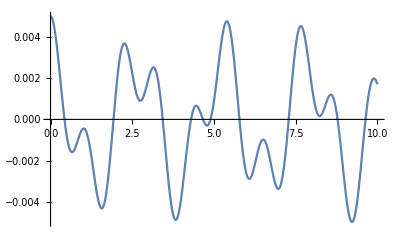

```mathematica
Plot[{α1*(θ1[t]/.Sapprox11[[1]])+α2*(θ1[t]/.Sapprox12)}/.{α1->2,α2->1.5,Subscript[θ11, 0]->0.001,Subscript[θ12, 0]->0.002},{t,0,10}]
```

```mathematica
Ω11=θ1[t]/.A[[1]] (*θ1[0]==Pi/2, θ2[0]==Pi/2, all masses and lengths unity, g==9.8*)
```

InterpolatingFunction[{{0., 50.}}, <>][t]

```mathematica
Ω12=θ1[t]/.A [[1]](*θ1[0]->Pi/3,θ2[0]==Pi/2, all masses and lengths unity, g==9.8*)
```

InterpolatingFunction[{{0., 50.}}, <>][t]

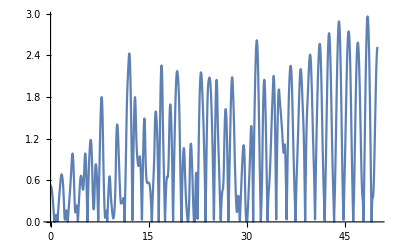

```mathematica
Plot[Abs[Ω12-Ω11],{t,0,50}]
(*Plot θ1^(2)[t]-θ1^(1)[t]*)
```

```mathematica
Ω21=θ2[t]/.A[[1]] (*θ1[0]==Pi/2, θ2[0]==Pi/2, all masses and lengths unity, g==9.8*)
```

InterpolatingFunction[{{0., 100.}}, <>][t]

```mathematica
Ω22=θ2[t]/.A[[1]] (*θ1[0]==Pi/2, θ2[0]==Pi/3, all masses and lengths unity, g==9.8*)
```

InterpolatingFunction[{{0., 100.}}, <>][t]

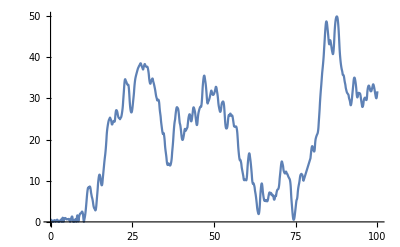

```mathematica
Plot[Abs[Ω21-Ω22],{t,0,100}]
(*Plot θ1^(2)[t]-θ1^(1)[t]*)
```

```mathematica
Animate[Show[ParametricPlot[{Subscript[l, 1] Sin[θ1[t]],-Subscript[l, 1]Cos[θ1[t]]}/.A[[1]]/.{Subscript[l, 1]->1},{t,0,time},PlotRange->{{-2.1,2.1},{-2.1,2.1}},PlotStyle->Red],
ParametricPlot[{Subscript[l, 1] Sin[θ1[t]]+Subscript[l, 2] Sin[θ2[t]],-Subscript[l, 1]Cos[θ1[t]]-Subscript[l, 2] Cos[θ2[t]]}/.A[[1]]/.{Subscript[l, 1]->1,Subscript[l, 2]->1},{t,0,time},PlotRange->{{-2.1,2.1},{-2.1,2.1}}]],{time,0,30}]
```

```mathematica
(*animation of the path of the 2 masses of the double pendulum for unit masses unit lengths, θ1[0]=θ2[0]=Pi/2, θ1'[0]=θ2'[0]=0., g=9.8*)
```